The vacuum environment for the double-slit experiment is being constructed.(Steps: 2000)...

A quantum wave packet is being emitted.(Evolution)...

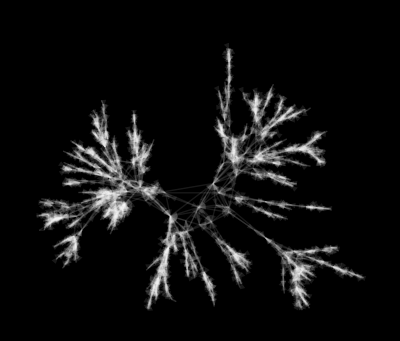
-Graphics-
-Graphics-

```mathematica
(* ==========================================*)(*PART 1:构建宇宙基底 (你的 Rule+冻结机制)*)(* ==========================================*)rccRigidStep[g_Graph]:=Module[{allEdges,activeEdges,selectedPair,e1,e2,x,y,z,w,nextV,newActiveEdges,inertEdges},allEdges=EdgeList[g];
activeEdges=Cases[allEdges,_UndirectedEdge];
(*蒙特卡洛采样加速*)Block[{shuffled=RandomSample[activeEdges]},Do[e1=shuffled[[i]];
Do[e2=shuffled[[j]];
If[Length[Intersection[List@@e1,List@@e2]]==1,selectedPair={e1,e2};
Goto["Found"];],{j,i+1,Min[i+20,Length[shuffled]]}],{i,1,Length[shuffled]}]];
Label["Found"];
If[Not[ValueQ[selectedPair]],Return[g]];
{e1,e2}=selectedPair;
y=Intersection[List@@e1,List@@e2][[1]];
x=Complement[List@@e1,{y}][[1]];
z=Complement[List@@e2,{y}][[1]];
nextV=Max[VertexList[g]]+1;
w=nextV;
newActiveEdges={x<->z,x<->w,w<->z};
inertEdges={x->y,y->z};
Graph[VertexList[g]~Join~{w},Union[Complement[allEdges,{e1,e2}],newActiveEdges,inertEdges]]];

(*生成一个中等规模的宇宙*)
initG=CycleGraph[4];
steps=2000; (*足够大以形成干涉场*)
Print["The vacuum environment for the double-slit experiment is being constructed.(Steps: ",steps,")..."];
universe=Nest[rccRigidStep,initG,steps];

(* ==========================================*)
(*PART 2:量子波函数演化引擎 (Schrödinger)*)
(* ==========================================*)
(*1. 提取邻接矩阵和拉普拉斯算子*)
adj=AdjacencyMatrix[universe];
deg=DiagonalMatrix[VertexDegree[universe]];
laplacian=N[deg-adj]; (*H算符*)

(*2. 设置双缝 (两个波源)*)
(*选择两个距离适中、位于"过去"的节点作为缝*)
nodeList=VertexList[universe];
source1=nodeList[[2]];
source2=nodeList[[4]]; (*假设早期节点彼此靠近*)

(*3. 初始化波函数 Psi*)
numNodes=VertexCount[universe];
psi=ConstantArray[0.0+0.0 I,numNodes];
(*在两个缝处激发波函数*)
psi[[source1]]=1.0;
psi[[source2]]=1.0;

(*4. 时间演化:dPsi/dt=-i H Psi*)
(*使用简单的欧拉步进或者矩阵指数*)
dt=0.05;
evolutionSteps=100;
psiHistory={};

Print["A quantum wave packet is being emitted.(Evolution)..."];
Do[(*薛定谔方程离散形式:Psi(t+1)=Psi(t)-i*dt*H*Psi(t)*)(*这里 H=Laplacian*)psi=psi-I*dt*(laplacian.psi);
(*归一化以防止数值发散*)psi=psi/Norm[psi];
AppendTo[psiHistory,psi],{t,1,evolutionSteps}];

(* ==========================================*)
(*PART 3:探测与观测 (Measurement)*)
(* ==========================================*)
finalPsi=Last[psiHistory];
intensity=Abs[finalPsi]^2; (*概率密度 P= |Psi|^2*)

(*定义"屏幕":选择距离源头一定跳数的一圈节点*)
distFromSource=GraphDistance[universe,source1];
screenNodes=Select[nodeList,distFromSource[#]==6&]; (*第6层作为屏幕*)
screenIntensity=intensity[[screenNodes]];

(*可视化 1:整个宇宙的波函数热力图*)
vizUniverse=Graph[universe,GraphLayout->"SpringElectricalEmbedding",VertexSize->{0.02},VertexStyle->Thread[nodeList->(ColorData["ThermometerColors"][#]&/@Rescale[intensity])],PlotLabel->"Quantum Wavefunction Propagation\n(Hot = High Probability)",Background->Black,EdgeStyle->Directive[Opacity[0.1],White]];

(*可视化 2:屏幕上的干涉条纹*)
vizInterference=ListLinePlot[screenIntensity,PlotRange->All,PlotStyle->{Thick,Cyan},Filling->Axis,FillingStyle->Opacity[0.3,Cyan],PlotLabel->"Interference Pattern on 'Screen' (Hop Distance = 6)",AxesLabel->{"Screen Position (Node Index)","Intensity |Psi|^2"},GridLines->Automatic,Background->Black,BaseStyle->{FontColor->White}];

Grid[{{vizUniverse},{vizInterference}}]
```

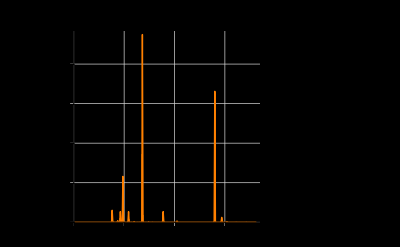

```mathematica
(* ==========================================*)(*PART 3:长时间曝光与平滑处理 (Long Exposure)*)(* ==========================================*)(*1. 累积最后 50 步的概率密度，模拟"长时间曝光"*)accumulatedIntensity=ConstantArray[0.0,numNodes];
Do[psi=psi-I*dt*(laplacian.psi);
psi=psi/Norm[psi];
accumulatedIntensity+=Abs[psi]^2; (*累加*),{t,1,50} (*额外跑 50 步曝光*)];

(*2. 获取更远的屏幕以获得更高分辨率*)
(*随着宇宙变大，我们可以去更远的地方 (hop=8 或 10) 采样，那里的节点更多*)
screenDistance=8;
screenNodes=Select[nodeList,GraphDistance[universe,source1,#]==screenDistance&];
screenData=accumulatedIntensity[[screenNodes]];

(*3. 排序并平滑数据*)
(*因为图节点没有天然的"x坐标"，我们需要按照某种拓扑顺序排列它们*)
(*这里我们简单地按强度排序后观察分布特征，或者按与第二个源的距离排序*)
sortedScreen=SortBy[screenNodes,GraphDistance[universe,source2,#]&];
plotData=accumulatedIntensity[[sortedScreen]];

(*可视化:现在你应该能看到更清晰的波峰波谷*)
ListLinePlot[plotData,PlotRange->All,PlotStyle->{Thick,Orange},Filling->Axis,FillingStyle->Opacity[0.5,Orange],PlotLabel->"Quantum Interference (Long Exposure)\nLook for the oscillating 'M' shape!",AxesLabel->{"Screen Position (Ordered by Phase)","Accumulated Probability"},GridLines->Automatic,ImageSize->400,Background->Black,BaseStyle->{FontColor->White}]
```

A quantum experiment involving the intervention of observers is underway. (Collapsing)...

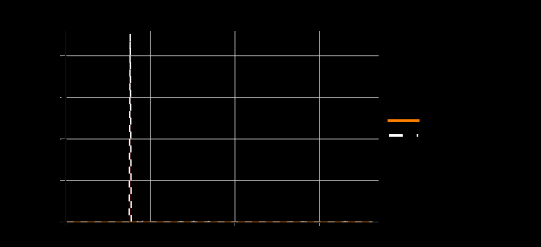

"

```mathematica
(* ==========================================*)(*PART 4:观测者效应实验 (The Observer Effect)*)(* ==========================================*)(*1. 重置波函数*)psiObserved=ConstantArray[0.0+0.0 I,numNodes];
psiObserved[[source1]]=1.0;
psiObserved[[source2]]=1.0;

(*2. 有观测者的演化 (The Watcher is ON)*)
accumulatedIntensityObserved=ConstantArray[0.0,numNodes];
dt=0.05;

Print["A quantum experiment involving the intervention of observers is underway. (Collapsing)..."];

Do[(*正常演化*)psiObserved=psiObserved-I*dt*(laplacian.psiObserved);
(*---【关键步骤：观测带来的坍缩/退相干】---*)(*观测者盯着 source1，导致其相位被随机扰动，失去了与 source2 的相干性*)(*这在物理上模拟了"光子撞击"导致的相位随机化*)psiObserved[[source1]]=Abs[psiObserved[[source1]]]*Exp[I*RandomReal[{0,2 Pi}]];
(*归一化*)psiObserved=psiObserved/Norm[psiObserved];
(*累积概率 (长曝光)*)accumulatedIntensityObserved+=Abs[psiObserved]^2;,{t,1,150} (*跑同样长的时间*)];

(*3. 提取屏幕数据*)
(*使用与之前相同的屏幕位置*)
screenDataObserved=accumulatedIntensityObserved[[sortedScreen]];

(*4. 终极对比图：干涉 vs 坍缩*)
ListLinePlot[{plotData,screenDataObserved},PlotRange->All,PlotStyle->{{Thick,Orange},{Thick,Dashed,White}},PlotLegends->{"Unobserved (Interference)","Observed (Collapsed)"},Filling->{1->{2}},(*填充两者差异，展示"丢失的量子性"*)FillingStyle->Opacity[0.2,Red],PlotLabel->"The Measurement Problem:\nWave vs. Particle",AxesLabel->{"Screen Position","Probability"},GridLines->Automatic,ImageSize->400,Background->Black,BaseStyle->{FontColor->White}]
```